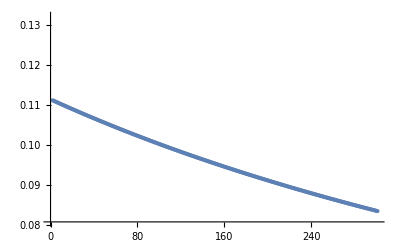

```mathematica
alpha = 0.01;
n0 = 900;
tMax = 300;
R = 1;

newN[n_] := R*n*Exp[-alpha*n];

data1 = NestList[R*#*Exp[-alpha*#] &, 900, 300];
ListPlot[data1]
```